```mathematica
convertValueTo01[x_,A_,B_]:=(x -A)/(B-A)
convertValueFrom01[x_,a_,b_]:=x(b-a) + a
convertValue2[x_,A_,B_,a_,b_]:=convertValueFrom01[convertValueTo01[x,A,B],a,b]
convertValue3[x_,A_,B_,C_,a_,b_,c_]:=If[x<B,convertValue2[x,A,B,a,b],convertValue2[x,B,C,b,c]]
```

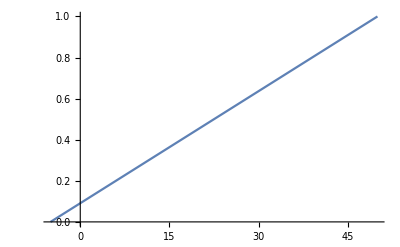

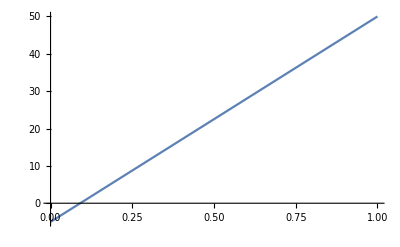

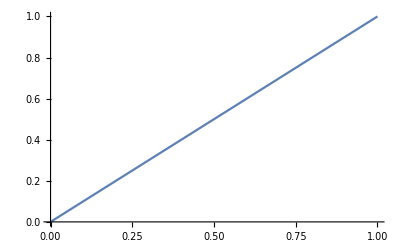

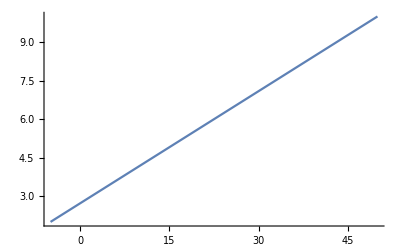

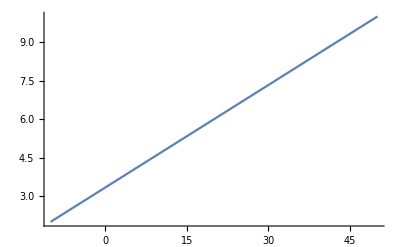

```mathematica
Plot[convertValueTo01[x,-5,50],{x,-5,50}]
Plot[convertValueFrom01[x,-5,50],{x,0,1}]
Plot[convertValueTo01[convertValueFrom01[x,-5,50],-5,50],{x,0,1}]
Plot[convertValue2[x,-5,50,2,10],{x,-5,50}]
Plot[convertValue3[x,-10,20,50,2,6,10],{x,-10,50}]
```

```mathematica
convertValue2[x,A,B,a,b]//FullSimplify //CForm
```

a + ((-a + b)*(-A + x))/(-A + B)